#### My Net Worth

At the end of each year I calculate my total net worth, and record it here. Note that I could not bear to even open the statements for 2008, let alone read them, so there is a gap for 2008.

```mathematica
actual = { {2005, 510551}, {2006, 636970}, {2007, 861102}, {2009, 826474}, {2010, 1027392}, {2011, 1075695}, {2012, 1238616}, {2013, 1670650}, {2014, 1934846}, {2015, 1939475} , {2016,2202582},{2017,2659917}};
```

Extract the first year, last year, value at first year, and value at last year.

```mathematica
startingValue = Last[First[actual]];
```

```mathematica
finalValue = Last[Last[actual]];
```

```mathematica
firstYear = First[First[actual]];
```

```mathematica
lastYear = First[Last[actual]];
```

```mathematica
years = lastYear - firstYear;
```

Solve for and print the rate of return that will turn the start value into the final value, running from the start year to the final year.

```mathematica
Print[100 i /. Solve[startingValue Exp[ years i] == finalValue, {i}, Reals] // N]
```

{13.7547}

Generate a ListPlot[] of the actual data.

```mathematica
p1 = ListPlot[actual];
```

Set up the compound interest formula, solve it, and plot the curve.

```mathematica
model = startingValue Exp[i (x-firstYear)];
```

```mathematica
iRule = FindFit[actual, model, {i}, x];
```

```mathematica
p2 =Plot[model /. iRule, {x, firstYear, lastYear}];
```

Plot actual, and the best compound interest fit.

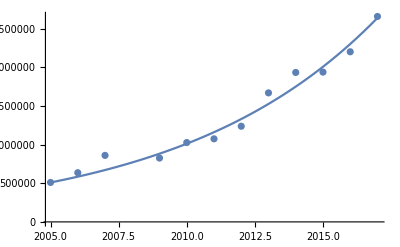

```mathematica
Show[p1, p2]
```

Extrapolate to the year 2022 (when I will be 70 years old).

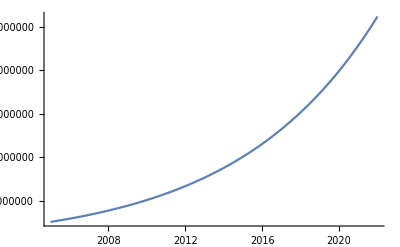

```mathematica
Plot[model /. iRule, {x, firstYear, 2022}]
```

And just for laughs, year 2052, when I will be 100 years old.

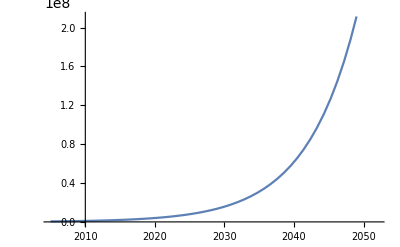

```mathematica
Plot[model /. iRule, {x, firstYear, 2052}]
```